# Final Project MATH299M - Are random numbers truly random?

This notebook will attempt to analyze many distribution of random numbers and determine whether or not the distributions are random. I predict that as we increase the number of random numbers used in the distribution, the more uniform the distribution will be. The term uniform here means that the distribution of observed frequencies will be close to the expected frequency. In this case, the expected frequencies are all the same which is why we say the distribution is uniform. For example, if we were to plot a histogram of expected frequencies for this first simulation, it would look like a rectangle as each random number should appear at least once because they all have an equal probability of appearing. However, due to random errors, this is not always the case and this is why we we can see discrepancies between observed and expected data, especially for small data sets. If you have ever been instructed to re-do an experiment or perform any experiment multiple times, it is because repetition reduces random error.

There will be a series of histograms below plotting the frequency at which a certain number appears for a given set of random integers. There are ten possibilities of random numbers that could appear and they are all single digits, 0 through 9. In addition, the probability that each number will appear are completely equal. So if we were to generate 10 random numbers, we would expect each single digit between 0 and 9 to appear one time. If we were to generate 100 random numbers, we would expect to each single digit between 0 and 9 to appear 10 ten times. Therefore, the expected probability for each random number is 10%. Multiply this 10% by the data size in order to get the expected frequency. Note that the data size is n for this case.

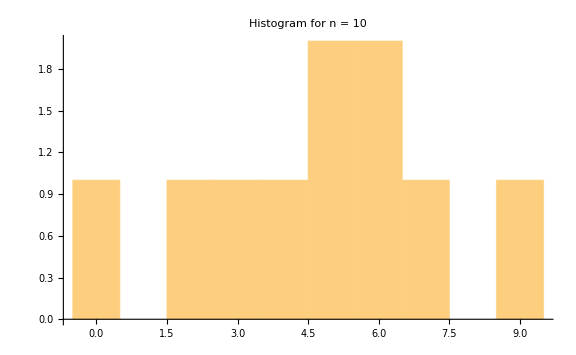
{0.03125,-Graphics-}

```mathematica
RandoInt101 = RandomInteger[9, 10];
Timing[Histogram[RandoInt101, {1},PlotLabel-> "Histogram for n = 10", ImageSize -> Large]]
```

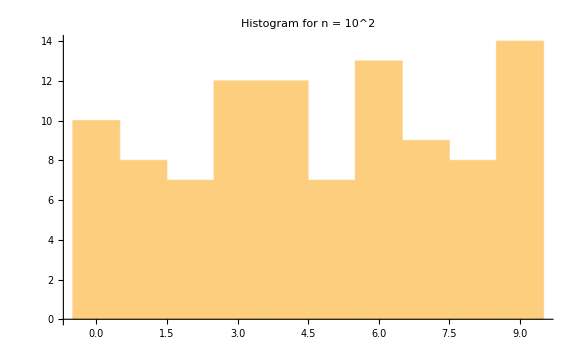
{0.046875,-Graphics-}

```mathematica
RandoInt102 = RandomInteger[9, 10^2];
Timing[Histogram[RandoInt102, {1},PlotLabel-> "Histogram for n = 10^2", ImageSize -> Large]]
```

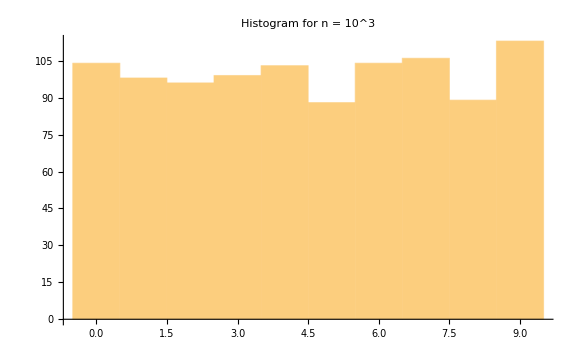
{0.015625,-Graphics-}

```mathematica
RandoInt103 = RandomInteger[9, 10^3];
Timing[Histogram[RandoInt103, {1},PlotLabel-> "Histogram for n = 10^3", ImageSize -> Large]]
```

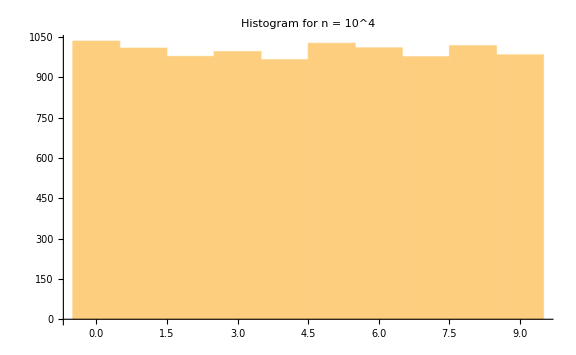
{0.078125,-Graphics-}

```mathematica
RandoInt104 = RandomInteger[9, 10^4];
Timing[Histogram[RandoInt104, {1},PlotLabel-> "Histogram for n = 10^4", ImageSize -> Large]]
```

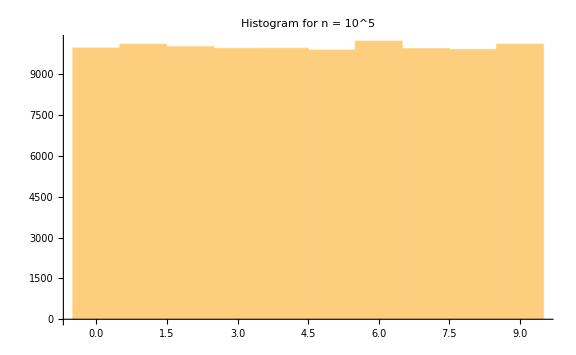
{0.140625,-Graphics-}

```mathematica
RandoInt105 = RandomInteger[9, 10^5];
Timing[Histogram[RandoInt105, {1},PlotLabel-> "Histogram for n = 10^5", ImageSize -> Large]]
```

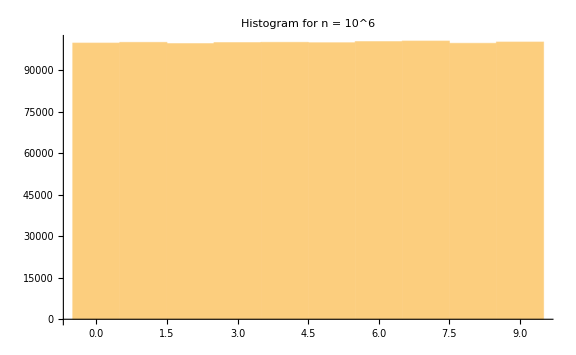
{1.03125,-Graphics-}

```mathematica
RandoInt106 = RandomInteger[9, 10^6];
Timing[Histogram[RandoInt106, {1},PlotLabel-> "Histogram for n = 10^6", ImageSize -> Large]]
```

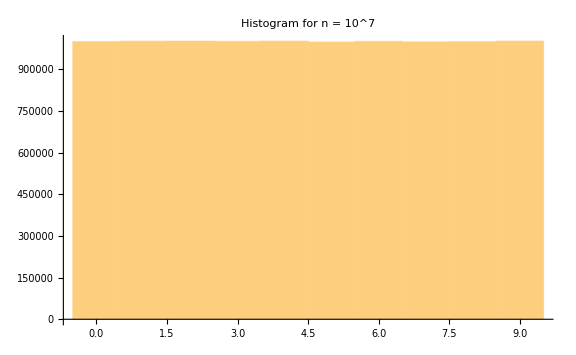
{9.51563,-Graphics-}

```mathematica
RandoInt107 = RandomInteger[9, 10^7];
Timing[Histogram[RandoInt107, {1},PlotLabel-> "Histogram for n = 10^7", ImageSize -> Large]]
```

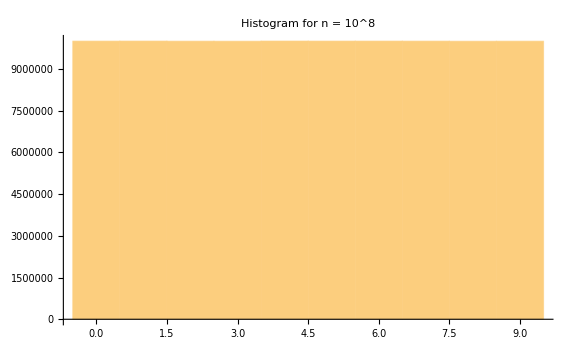
{120.719,-Graphics-}

```mathematica
RandoInt108 = RandomInteger[9, 10^8];
Timing[Histogram[RandoInt108, {1},PlotLabel-> "Histogram for n = 10^8", ImageSize -> Large]]
```

# Chi-Squared Analysis

These last few histograms are very uniform and it is quite impressive how “rectangular” they are. The first few histograms, however, are not nearly as rectangular and I would like to explore this further by performing a chi squared analysis on each histogram. In order to properly perform a Chi-Squared analysis, we need to have a null hypothesis and specify our degrees of freedom.

Null Hypothesis: There is no statistically significant difference between the observed and the expected frequencies. Therefore, if we reject our null hypothesis, then there is a statistically significant difference between the observed and expected frequencies and the data is not in good agreement with theory.

Degrees of Freedom = Number of Data Points - Number of Fitting Parameters = 10 - 0 = 10

-Graphics-
Sample Calculation of Chi-Squared (see whiteboard in classroom):

```mathematica
HistogramList[RandoInt101,{1}]
```

{{-0.5,0.5,1.5,2.5,3.5,4.5,5.5,6.5,7.5,8.5,9.5},{1,3,1,0,3,0,0,0,0,2}}

```mathematica
ObservedFrequencyData101={{0,1,2,3,4,5,6,7,8,9},{1/10,3/10,1/10,0/10,3/10,0/10,0/10,0/10,0/10,2/10}}
ExpectedFrequencyData101={{0,1,2,3,4,5,6,7,8,9},{1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10}}
```

{{0,1,2,3,4,5,6,7,8,9},{1/10,3/10,1/10,0,3/10,0,0,0,0,1/5}}

{{0,1,2,3,4,5,6,7,8,9},{1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10}}

-Graphics-

```mathematica
PearsonChiSquareTest[RandoInt101,UniformDistribution[],"HypothesisTestData"]
```

HypothesisTestData[…]

Now, I will perform chi-squared tests for the rest of the data sets and see whether or not we still accept or reject the null hypothesis.

```mathematica
PearsonChiSquareTest[RandoInt102,UniformDistribution[],"HypothesisTestData"]
```

HypothesisTestData[…]

```mathematica
PearsonChiSquareTest[RandoInt103,UniformDistribution[],"HypothesisTestData"]
```

HypothesisTestData[…]

```mathematica
PearsonChiSquareTest[RandoInt104,UniformDistribution[],"HypothesisTestData"]
```

HypothesisTestData[…]

```mathematica
PearsonChiSquareTest[RandoInt105,UniformDistribution[],"HypothesisTestData"]
```

HypothesisTestData[…]

```mathematica
PearsonChiSquareTest[RandoInt106,UniformDistribution[],"HypothesisTestData"] (*8 MB worth of data*)
```

HypothesisTestData[…]

```mathematica
PearsonChiSquareTest[RandoInt107,UniformDistribution[],"HypothesisTestData"](*80 MB worth of data*)
```

HypothesisTestData[…]

```mathematica
PearsonChiSquareTest[RandoInt108,UniformDistribution[],"HypothesisTestData"](*800 MB worth of data*)
```

HypothesisTestData[…]

So, other the first test, we have rejected our null hypothesis. We rejected our null hypothesis because the p-value is incredibly small. I will discuss the p-value further and what it means below.

P-Value:

-Graphics-

-Graphics-

```mathematica
Animate[Plot[PDF[ChiSquareDistribution[v],x],{x,0,30},PlotRange->{0,1}],{v,1,20},AnimationRunning->False]
```

# Storage

The last three tests actually asked if I wanted to store the data from the Hypothesis Test. Mathematica asked for me to store it because the data file was so large, it was 

-Graphics-

# Computation Time

Next, I want to mention how the computation time changes as we increase the number of random numbers generated. The first few tests were practically instantaneous, and the difference in computation time from 10 random numbers to 10^4 random numbers is negligible. I consider this difference negligible because the Timing function in Mathematica has some error and is not completely accurate. For example, if I were to recompute the first few histograms multiple times, I would get a different computation time about half the time. In addition, I was also able to get the computation time to be longer for 10^2 random numbers than 10^3 random numbers (0.046875 seconds vs 0.03125 seconds). I am not sure why this was able to happen, but there are a lot of factors that are involved that could have got in the way. Some of these factors are: (1) the amount of memory available on my machine when I run the command, (2) the accuracy and precision of the Timing function built in to Mathematica, and (3) random error. Regardless, the first few computation times are just supposed to tell us that they are practically instantaneous.

The computation time notably increased around 10^5 random numbers, doubling the computation time from 10^4 random numbers (0.0625 seconds to 0.125 seconds). Then the next three tests increased about 10 fold each time. Specifically, the computation times from 10^5 to 10^8 were 0.125 seconds, 1.09375 sec, 10.1719 sec, and 101.031 sec. The increase in times (in terms of multiplicative difference) were approximately 8.75 times, 9.3 times, and 9.93 times. Remarkably, the data for these computation times definitely appears to be logarithmic.

Finally, I also tried computing 10^9 random numbers, (which should have taken about 15 minutes!!!), but my computer was not able to handle it and it had a very hard time being operable when it was running this command. So, for some reason 10^9 is a critical point for an AMD Laptop with 8 GB of RAM, who knew?

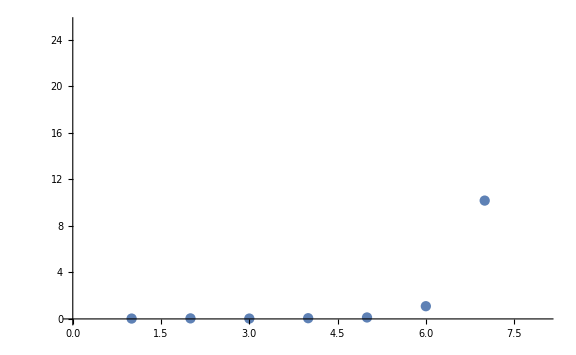

```mathematica
DataSet1={{1,0.03125},{2,0.046875},{3,0.03125},{4,0.0625},{5,0.125}, {6,1.09375},{7,10.1719},{8,101.031}};
ListPlot[DataSet1, ImageSize-> Large]
```

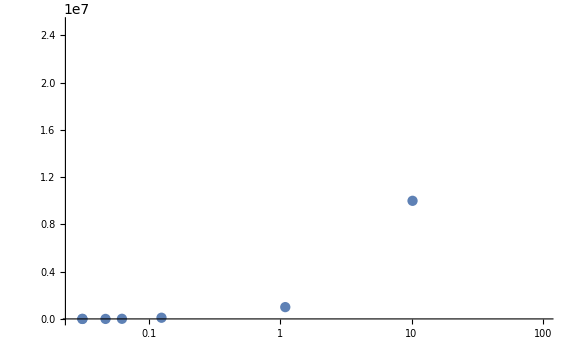

```mathematica
DataSet2={{0.03125,10},{0.046875,10^2},{0.03125,10^3},{0.0625,10^4},{0.125,10^5},{1.09375,10^6},{10.1719,10^7},{101.031, 10^8}};
ListLogLinearPlot[DataSet2, ImageSize-> Large]
```

Nick Emm - University of Maryland, College Park
MATH299M/CMSC389W Fall 2018
December 15th, 2018